```mathematica
CleanThisNotebook[]:=Module[{nb,contents,newcontents},
nb=EvaluationNotebook[];
SetOptions[nb,
"TrackCellChangeTimes"->False
,PrivateNotebookOptions->{"FileOutlineCache"->False}];
];(*CleanThisNotebook[]; *)(* just run once to clean for Github *)
SetOptions[EvaluationNotebook[],
"NotebookAutoSave"->False
];
```

```mathematica
SetDirectory[NotebookDirectory[]];
Get["PlotStylings.m"];
Get["LocateParastichyExample91.mx"]; (* this file has both an example image and the parastichy families this notebook recomputes *)
Get["ImageParastichy.m"];
```

## View image

```mathematica
sunflower= LocateParastichyExample91["Image"];
(*Show[sunflower,ImageSize->Small]*)
```

## Parastichy display functions

```mathematica
paraToLine[meshAssociation_,paraline_] := Block[{x},Line[ MeshPrimitives[meshAssociation["Mesh"],{0,paraline}] /. Point[x_]->x]];

showMeshPara[meshAssociation_,paraFamilies_,highlightPoints_,labelPoints_] := Module[{allLines,familyLines,meshxy,meshPoint,nodeLabel,nodeLabelText,nodeLabels},
familyLines[paraFamily_] :=  Map[ 
{
{
If[Mod[#["Index"],10]==0 || #["Index"]==Length[paraFamily],Thickness[Medium],Directive[{Thin}]]
,paraToLine[meshAssociation,#["Members"]]
}
,familyLabels[paraFamily]
}&,paraFamily];

familyLabels[paraFamily_] :=  Map[ 
Text[#["Index"],meshxy[#["Head"]]]&,paraFamily];


(*nodeLabel[parastichy_] := parastichy["Head"];
nodeLabelText[parastichyFamily_] := Map[Text[#,meshxy[#]]&,Map[nodeLabel,parastichyFamily]];
parastichyLabels = nodeLabelText /@ paraFamilies;
*)
allLines = MapIndexed[{jParastichyColour[First[#2]],familyLines[#1]}&,paraFamilies];

meshPoint[node_] := MeshPrimitives[meshAssociation["Mesh"],{0,node}];
meshxy[node_] := meshPoint[node] /. Point[x_]-> x;


Graphics[{
{Thin,LightGray,PointSize[Medium],MeshPrimitives[meshAssociation["Mesh"],1]}
,{Red,allLines}
,MapIndexed[{PointSize[Large],jParastichyColour[First[#2]], MeshPrimitives[meshAssociation["Mesh"],{0,#1}]}&,highlightPoints]
,{Map[Text[#,meshxy[#]]&, labelPoints] }

}]
];
```

## First round

Dropping 5 points as duplicates

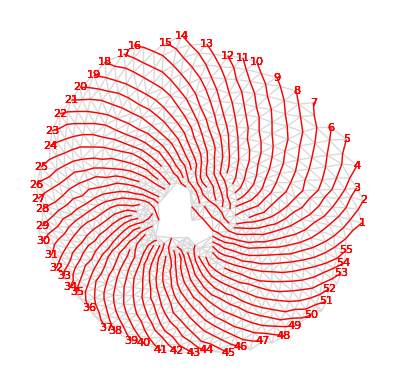

```mathematica
coordinates  = LocateParastichyExample91["SeedCoordinates"];
m91 = makeTidyMesh[coordinates];
locateParastichyOptions["StraightnessWhenAdjacent"] =25;
locateParastichyOptions ["ParastichyExtensionLength"]=  5;
locateParastichyOptions ["InitialParastichyLength"]=  5;
locateParastichyOptions ["FamilyGrowthSize"] =  90;
mpf2=createParastichyFamily[m91,{2,5}];
showMeshPara[m91,{mpf2 },{},{}]
```